{{x→2.17109}}

{{1.53094,0.372585},{1.61049,0.482981},{1.67606,0.557498},{1.73075,0.629255},{1.78193,0.703772},{1.82821,0.805888},{1.87136,0.872125},{1.91416,0.974241},{1.9443,1.0598},{1.98268,1.14259},{2.00698,1.20883},{2.03573,1.31923},{2.06361,1.41858},{2.08706,1.51242},{2.11045,1.68077},{2.13618,1.82705},{2.15637,2.11684},{2.17693,2.73229},{2.17882,2.81509},{2.18134,2.5667},{2.1915,2.34591},{2.18768,2.13339},{2.18895,1.54554},{2.19214,1.18675},{2.19341,1.10948},{2.2011,1.0046},{2.20756,0.954922},{2.21992,0.833487},{2.23043,0.800368},{2.24439,0.725851},{2.25447,0.662374}}

0.716172

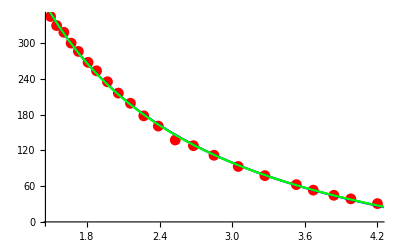

| Estimate | Standard Error | t-Statistic | P-Value
a | 51.9875 | 2.52496 | 20.5895 | 2.07042×10^-12
b | -79.276 | 4.84489 | -16.3628 | 5.65387×10^-11

| Estimate | Standard Error | t-Statistic | P-Value
a | 2387.87 | 140.675 | 16.9744 | 9.37824×10^-10
b | -5150.69 | 309.992 | -16.6156 | 1.20019×10^-9

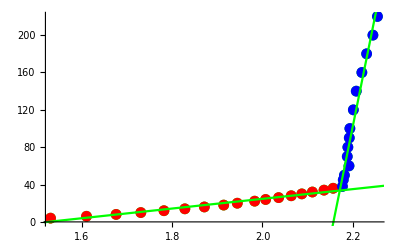

```mathematica
Filename = "abkuehlen"; 
Filepath = StringJoin[NotebookDirectory[], "../data/"]; 

rawData = Import[StringJoin[Filepath, Filename, ".txt"], "Table"] ;
partitionedData = Drop[rawData, 1][[All,{1,2}]];

aufwaermData = Import[StringJoin[Filepath, "aufwaermen", ".txt"], "Table"] ;
partitionedAufwaermData = Drop[aufwaermData, 1][[All,{1,2}]];
aufwaermTData = Map[{753.24/(#1[[2]]+151.71),#1[[1]]}&, partitionedAufwaermData];
vorLambda = Take[aufwaermTData,17];
nachLambda = Drop[aufwaermTData,17];

nlmCurie = NonlinearModelFit[partitionedData, C/T + Subscript[U, 0], {C, Subscript[U, 0]}, T];
nlmCurieWeiss=NonlinearModelFit[partitionedData, C/(T-θ) + Subscript[U, 0], {{C,700}, {Subscript[U, 0],-150},{θ,0}}, T];

nlmCurie["ParameterTable"];
nlmCurieWeiss["ParameterTable"];

nlmVorLambda = NonlinearModelFit[vorLambda,a*x + b, {a, b}, x];
nlmnachLambda = NonlinearModelFit[nachLambda, a*x + b, {a, b},x];



Solve[nlmnachLambda["BestFit"] == nlmVorLambda["BestFit"], x]


SpezifischeWärme = {{1.53094,135},{1.61049,175},{1.67606,202},{1.73075,228},{1.78193,255},{1.82821,292},{1.87136,316},{1.91416,353},{1.9443,384},{1.98268,414},{2.00698,438},{2.03573,478},{2.06361,514},{2.08706,548},{2.11045,609},{2.13618,662},{2.15637,767},{2.17693,990},{2.17882,1020},{2.18134,930},{2.1915,850},{2.18768,773},{2.18895,560},{2.19214,430},{2.19341,402},{2.2011,364},{2.20756,346},{2.21992,302},{2.23043,290},{2.24439,263},{2.25447220,240}};
SpezifischeWärme = Map[{#1[[1]],#1[[2]]*0.00275989}&, SpezifischeWärme]
SpezifischeWärme = Total[(First[#2]-First[#1])*0.5*(Last[#1]+Last[#2])&@@@ Partition[SpezifischeWärme,2,1]]

(*Wärme = Total[Map[0.5*#1[[1]]*#1[[2]]&, SpezifischeWärme]]*)



Show[ListPlot[partitionedData, PlotStyle -> Red],Plot[{nlmCurieWeiss["BestFit"]},{T,1,5}, PlotStyle-> Blue], Plot[{nlmCurie["BestFit"]},{T,1,5}, PlotStyle-> Green]]

nlmVorLambda["ParameterTable"]
nlmnachLambda["ParameterTable"]

Show[ListPlot[aufwaermTData, PlotStyle -> Green],ListPlot[vorLambda, PlotStyle -> Red], ListPlot[nachLambda, PlotStyle -> Blue],

Plot[{nlmVorLambda["BestFit"]},{x,1,5}, PlotStyle-> Green], Plot[{nlmnachLambda["BestFit"]},{x,1,5}, PlotStyle-> Green]]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 51.9875 | 11.0935 | 4.68629 | 0.0000707709
b | -79.276 | 21.2863 | -3.72427 | 0.000913557
c | 2387.87 | 95.1628 | 25.0925 | 3.02176×10^-20
k | 2.17109 | 0.00223483 | 971.479 | 6.99497×10^-63

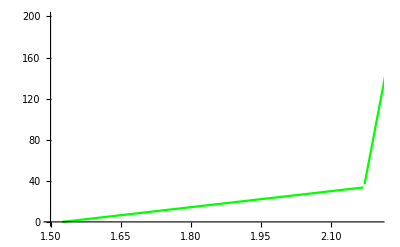

\begin{cases}
 a x+b & x<k \\
 k (a-c)+b+c x & x\geq k
\end{cases}

```mathematica
g[x_,a_,b_,c_,k_]:=Piecewise[{{a x+b,x<k},{b+(a-c) k+c x,x≥k}}];
nlm=NonlinearModelFit[aufwaermTData,g[x,a,b,c,k],{{a,52},{b,-80},{c,2388},{k,2.17}},x];
nlm["ParameterTable"]
Plot[{nlm["BestFit"]},{x,1,5}, PlotStyle-> Green,PlotRange->{{1.5,2.2},{0,200}}]
TeXForm[g[x,a,b,c,k]]
```